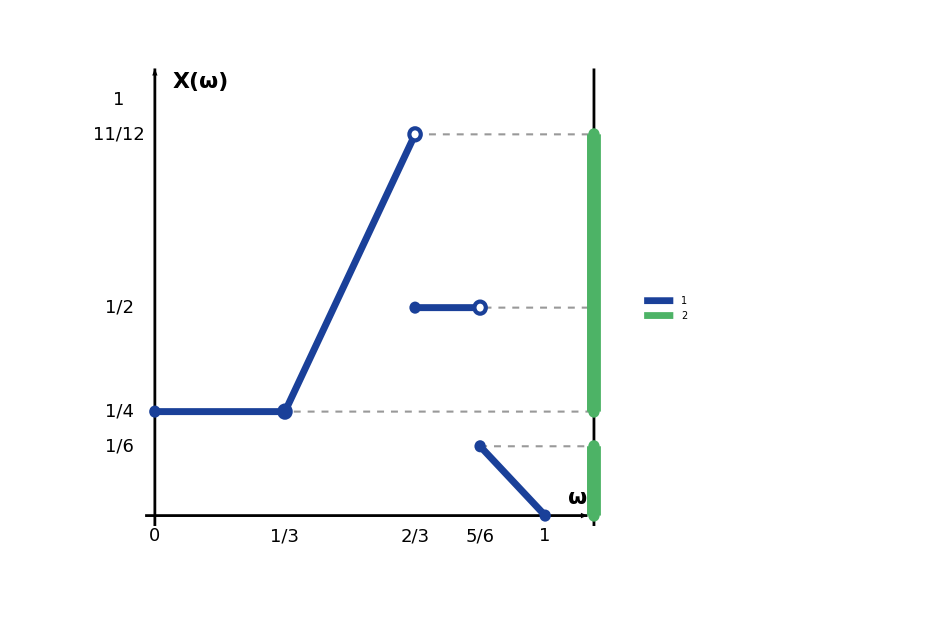

```mathematica
ClearAll[colX, colIm, r, xC, cerrado, abierto, ejes, trozos, guias, ejeCod, etiquetas, grafico1, diagrama1];

colX = RGBColor[0.1, 0.25, 0.6];      (* gráfica de X *)
colIm = RGBColor[0.3, 0.7, 0.4];     (* imagen de X *)
r = 0.35;
xC = 27;                              (* eje del codominio a la derecha *)

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

(* Escala: 24 unidades por unidad real *)
ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {26.6, 0}}], Arrow[{{0, -0.6}, {0, 25.8}}]} ;

(* Tramos de X:
   [0, 8) -> 6
   [8, 16) -> 2ω - 10 (de {8,6} a {16,22})
   [16, 20) -> 12
   [20, 24] -> 24 - ω (de {20,4} a {24,0}) *)
trozos = {colX, AbsoluteThickness[5],
   Line[{{0, 6}, {8, 6}}], Line[{{8, 6}, {16, 22}}],
   Line[{{16, 12}, {20, 12}}], Line[{{20, 4}, {24, 0}}],
   
   cerrado[{0, 6}, colX], abierto[{8, 6}, colX],
   cerrado[{8, 6}, colX], abierto[{16, 22}, colX],
   cerrado[{16, 12}, colX], abierto[{20, 12}, colX],
   cerrado[{20, 4}, colX], cerrado[{24, 0}, colX]};

guias = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{20, 4}, {xC, 4}}], Line[{{0, 6}, {xC, 6}}],
   Line[{{16, 12}, {xC, 12}}], Line[{{16, 22}, {xC, 22}}]};

(* Imagen de X = [0, 4] ∪ [6, 22] *)
ejeCod = {Black, AbsoluteThickness[2], Line[{{xC, -0.6}, {xC, 25.8}}],
   colIm, AbsoluteThickness[10], CapForm["Butt"],
   Line[{{xC, 0}, {xC, 4}}], Line[{{xC, 6}, {xC, 22}}],
   cerrado[{xC, 0}, colIm], cerrado[{xC, 4}, colIm],
   cerrado[{xC, 6}, colIm], cerrado[{xC, 12}, colIm],
   cerrado[{xC, 22}, colIm]};

etiquetas = {Black,
   Table[Text[Style[p[[2]], 18], {p[[1]], -1.2}],
    {p, {{0, "0"}, {8, "1/3"}, {16, "2/3"}, {20, "5/6"}, {24, "1"}}}] ,
   Table[Text[Style[p[[2]], 18], {-2.2, p[[1]]}],
    {p, {{4, "1/6"}, {6, "1/4"}, {12, "1/2"}, {22, "11/12"}, {24, "1"}}}] ,
   Text[Style["ω", 22, Bold], {26.0, 1.0}],
   Text[Style["X(ω)", 22, Bold], {2.8, 25.0}]};

grafico1 = Graphics[{guias, ejes, trozos, ejeCod, etiquetas},
   PlotRange -> {{-4.5, 28.5}, {-2.6, 26.5}}, ImageSize -> 700];

diagrama1 = Legended[grafico1,
   SwatchLegend[{colX, colIm}, {"gráfica de X", "imagen de X"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama1

Export[CloudObject["T3_PAd1_grafica"], diagrama1, "PNG", Background -> None, ImageResolution -> 300];
```

```mathematica
ClearAll[yTop, yBot, colO, colN, colA0, colA1, colCont, rr, cerrado, abierto, baseArriba, baseAbajo,
  pieza, segTop, barraTop, intervaloAbajo, llaveArriba, leyendaCon, caso, mapeo, casosA];

yTop = 4; yBot = 0;
colO = RGBColor[0.2, 0.55, 0.85];      (* antiimagen *)
colN = RGBColor[0.95, 0.6, 0.15];     (* intervalo de llegada [0,x] *)
colA0 = RGBColor[0.85, 0.25, 0.3];     (* rama \[Aacute]tomo 1/4 *)
colA1 = RGBColor[0.55, 0.1, 0.2];      (* rama \[Aacute]tomo 1/2 *)
colCont = RGBColor[0.55, 0.3, 0.75];   (* tramos continuos/lineales *)
rr = 0.22;

cerrado[p_, col_] := {col, Disk[p, rr]};
abierto[p_, col_] := {White, Disk[p, rr], col, AbsoluteThickness[3], Circle[p, rr]};

baseArriba = {{Black, AbsoluteThickness[4], Line[{{0, yTop}, {24, yTop}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yTop - 0.2}, {p[[1]], yTop + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yTop + 0.75}]},
    {p, {{0, "0"}, {8, "1/3"}, {16, "2/3"}, {20, "5/6"}, {24, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.6, yTop}]};

baseAbajo = {{Black, AbsoluteThickness[4], Line[{{0, yBot}, {24, yBot}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yBot - 0.2}, {p[[1]], yBot + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yBot - 0.75}]},
    {p, {{0, "0"}, {4, "1/6"}, {6, "1/4"}, {12, "1/2"}, {22, "11/12"}, {24, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.6, yBot}]};

pieza[t1_, t2_, b1_, b2_, col_: colO] := {
   {col, Opacity[0.12], Polygon[{{t1, yTop}, {t2, yTop}, {b2, yBot}, {b1, yBot}}]},
   {col, AbsoluteThickness[2.5],
    Table[Line[{{t1 + s (t2 - t1), yTop}, {b1 + s (b2 - b1), yBot}}],
     {s, {0, 0.25, 0.5, 0.75, 1}}]}
};

segTop[{x1_, c1_, x2_, c2_}, col_: colO] := {col, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{x1, yTop}, {x2, yTop}}],
   If[c1, cerrado[{x1, yTop}, col], abierto[{x1, yTop}, col]],
   If[c2, cerrado[{x2, yTop}, col], abierto[{x2, yTop}, col]]};

barraTop[x1_, x2_, col_] := {col, AbsoluteThickness[9], CapForm["Butt"], Line[{{x1, yTop}, {x2, yTop}}]};

intervaloAbajo[{a_, ca_, b_, cb_}, etqs_List] := {colN, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{a, yBot}, {b, yBot}}],
   If[ca, cerrado[{a, yBot}, colN], abierto[{a, yBot}, colN]],
   If[cb, cerrado[{b, yBot}, colN], abierto[{b, yBot}, colN]],
   Table[Text[Style[e[[2]], 20, Bold, Darker[colN, 0.3]], {e[[1]], yBot - 1.6}], {e, etqs}]};

leyendaCon[txt_] := SwatchLegend[{colO, colN}, {"antiimagen", txt},
   LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20];

caso[arr_, pre_List, piezas_List, etqs_List, txtLey_] := Legended[
   Graphics[{baseArriba, baseAbajo,
     Table[pieza @@ p, {p, piezas}],
     Table[segTop[p], {p, pre}],
     intervaloAbajo[arr, etqs]},
    PlotRange -> {{-6.5, 26.5}, {yBot - 2.6, yTop + 1.7}}, ImageSize -> 1100],
   leyendaCon[txtLey]];

(* Mapeo global por ramas *)
mapeo = Legended[
   Graphics[{baseArriba, baseAbajo,
     pieza[0, 8, 6, 6, colA0], pieza[8, 16, 6, 22, colCont],
     pieza[16, 20, 12, 12, colA1], pieza[20, 24, 4, 0, colCont],
     barraTop[0, 8, colA0], barraTop[8, 16, colCont],
     barraTop[16, 20, colA1], barraTop[20, 24, colCont],
     cerrado[{0, yTop}, colA0], cerrado[{24, yTop}, colCont],
     {colCont, AbsoluteThickness[9], CapForm["Butt"], Line[{{0, yBot}, {4, yBot}}], Line[{{6, yBot}, {22, yBot}}]},
     cerrado[{0, yBot}, colCont], cerrado[{4, yBot}, colCont],
     cerrado[{6, yBot}, colCont], cerrado[{22, yBot}, colCont],
     {colA0, Disk[{6, yBot}, 0.3]}, {colA1, Disk[{12, yBot}, 0.3]}},
    PlotRange -> {{-6.5, 26.5}, {yBot - 2.2, yTop + 1.7}}, ImageSize -> 1100],
   SwatchLegend[{colA0, colA1, colCont}, {"átomo 1/4", "átomo 1/2", "tramos continuos"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

(* Casos del apartado a *)
casosA = {
   (* 1. 0 <= x < 1/6 (x = 1/12 -> coord 2) *)
   caso[{0, True, 2, True}, {{22, True, 24, True}},
    {{22, 24, 2, 0}}, {{2, "x"}}, "intervalo [0,x]"],
   
   (* 2. 1/6 <= x < 1/4 (x = 5/24 -> coord 5) *)
   caso[{0, True, 5, True}, {{20, True, 24, True}},
    {{20, 24, 4, 0}}, {{5, "x"}}, "intervalo [0,x]"],
   
   (* 3. 1/4 <= x < 1/2 (x = 1/3 -> coord 8) *)
   caso[{0, True, 8, True}, {{0, True, 9, True}, {20, True, 24, True}},
    {{0, 8, 6, 6}, {8, 9, 6, 8}, {20, 24, 4, 0}}, {{8, "x"}}, "intervalo [0,x]"],
   
   (* 4. 1/2 <= x < 11/12 (x = 3/4 -> coord 18) *)
   caso[{0, True, 18, True}, {{0, True, 14, True}, {16, True, 24, True}},
    {{0, 8, 6, 6}, {8, 14, 6, 18}, {16, 20, 12, 12}, {20, 24, 4, 0}}, {{18, "x"}}, "intervalo [0,x]"],
   
   (* 5. 11/12 <= x <= 1 (x = 1 -> coord 24) *)
   caso[{0, True, 24, True}, {{0, True, 24, True}},
    {{0, 8, 6, 6}, {8, 16, 6, 22}, {16, 20, 12, 12}, {20, 24, 4, 0}}, {{24, "x=1"}}, "intervalo [0,x]"]
};

Export[CloudObject["T3_PAd1_a"], mapeo, "PNG", Background -> None, ImageResolution -> 300];
Do[Export[CloudObject["T3_PAd1_a" <> ToString[k]], casosA[[k]], "PNG", Background -> None, ImageResolution -> 300], {k, 1, 5}];
```

```mathematica
ClearAll[llaveArriba, casosBC];

llaveArriba[xa_, xb_, tL_, tP_] := Module[{y0 = yTop + 1.45, m = (xa + xb)/2},
   {colO, AbsoluteThickness[3],
    Line[{{xa, y0}, {xa, y0 + 0.3}, {m - 0.35, y0 + 0.3}, {m, y0 + 0.75},
      {m + 0.35, y0 + 0.3}, {xb, y0 + 0.3}, {xb, y0}}],
    Text[Style["λ = " <> tL, 22, Bold, Darker[colO, 0.3]], {m, y0 + 1.5}],
    Text[Style["P = " <> tP, 22, Bold, Darker[colO, 0.3]], {m, y0 + 2.5}]}];

casoConLlave[arr_, pre_List, piezas_List, etqs_List, llave_, txtLey_] := Legended[
   Graphics[{baseArriba, baseAbajo,
     Table[pieza @@ p, {p, piezas}],
     Table[segTop[p], {p, pre}],
     intervaloAbajo[arr, etqs],
     If[llave === None, {}, llaveArriba @@ llave]},
    PlotRange -> {{-6.5, 26.5}, {yBot - 2.6, yTop + 5.8}}, ImageSize -> 1100],
   leyendaCon[txtLey]];

casosBC = {
   (* 1. Intervalo [0, 1/3] (coord 8) *)
   casoConLlave[{0, True, 8, True}, {{0, True, 9, True}, {20, True, 24, True}},
    {{0, 8, 6, 6}, {8, 9, 6, 8}, {20, 24, 4, 0}}, {{8, "1/3"}},
    {0, 9, "13/24", "6553/13824"}, "intervalo"],
   
   (* 2. Intervalo [1/4, 3/4] (coords [6, 18]) *)
   casoConLlave[{6, True, 18, True}, {{0, True, 14, True}, {16, True, 20, True}},
    {{0, 8, 6, 6}, {8, 14, 6, 18}, {16, 20, 12, 12}}, {{6, "1/4"}, {18, "3/4"}},
    {0, 14, "3/4", "277/576"}, "intervalo"]
};

Do[Export[CloudObject["T3_PAd1_bc" <> ToString[k]], casosBC[[k]], "PNG", Background -> None, ImageResolution -> 300], {k, 1, 2}];
```

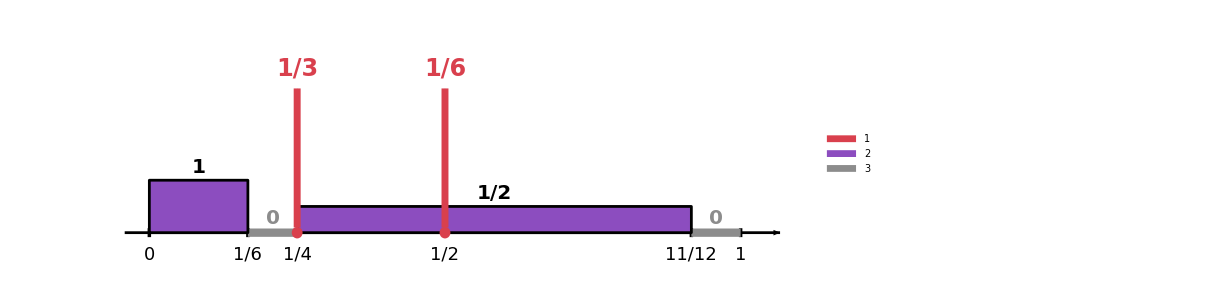

```mathematica
ClearAll[colDens, colAt, colCero, hD, yA, r, ejeBase, dens, ceros, atomos, grafico3, diagrama3];

colDens = RGBColor[0.55, 0.3, 0.75];   (* masa continua / densidad *)
colAt = RGBColor[0.85, 0.25, 0.3];     (* masa puntual / átomos *)
colCero = GrayLevel[0.55];            (* intervalos con masa 0 *)
hD = 2.0;                              (* altura para densidad 1 *)
yA = 5.5;                              (* altura de flechas para masas puntuales *)
r = 0.22;

ejeBase = {Black, AbsoluteThickness[2], Arrowheads[0.025], Arrow[{{-1, 0}, {25.6, 0}}],
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], -0.17}, {p[[1]], 0.17}}],
     Text[Style[p[[2]], 18], {p[[1]], -0.85}]},
    {p, {{0, "0"}, {4, "1/6"}, {6, "1/4"}, {12, "1/2"}, {22, "11/12"}, {24, "1"}}}]};

(* Densidad 1 en [0, 1/6] y densidad 1/2 en [1/4, 11/12] *)
dens = {colDens, EdgeForm[{Black, AbsoluteThickness[2]}],
   Rectangle[{0, 0}, {4, hD}],
   Rectangle[{6, 0}, {22, hD/2}],
   Black,
   Text[Style["1", 20, Bold], {2, hD + 0.5}],
   Text[Style["1/2", 20, Bold], {14, hD/2 + 0.5}]};

ceros = {colCero, AbsoluteThickness[6], CapForm["Butt"],
   Line[{{4, 0}, {6, 0}}], Line[{{22, 0}, {24, 0}}],
   Text[Style["0", 20, Bold, colCero], {5, 0.55}],
   Text[Style["0", 20, Bold, colCero], {23, 0.55}]};

(* Masas puntuales: 1/3 en x=1/4 (coord 6) y 1/6 en x=1/2 (coord 12) *)
atomos = {
   {colAt, AbsoluteThickness[5], Arrowheads[0.035],
    Arrow[{{6, 0.2}, {6, yA}}], Disk[{6, 0}, r],
    Text[Style["1/3", 24, Bold, colAt], {6, yA + 0.75}]},
   {colAt, AbsoluteThickness[5], Arrowheads[0.035],
    Arrow[{{12, 0.2}, {12, yA}}], Disk[{12, 0}, r],
    Text[Style["1/6", 24, Bold, colAt], {12, yA + 0.75}]}
};

grafico3 = Graphics[{ejeBase, dens, ceros, atomos},
   PlotRange -> {{-1.8, 26.2}, {-1.8, 7.8}}, ImageSize -> 900];

diagrama3 = Legended[grafico3,
   SwatchLegend[{colAt, colDens, colCero}, {"masa puntual", "densidad", "masa 0"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama3

Export[CloudObject["T3_PAd1_PX"], diagrama3, "PNG", Background -> None, ImageResolution -> 300];
```

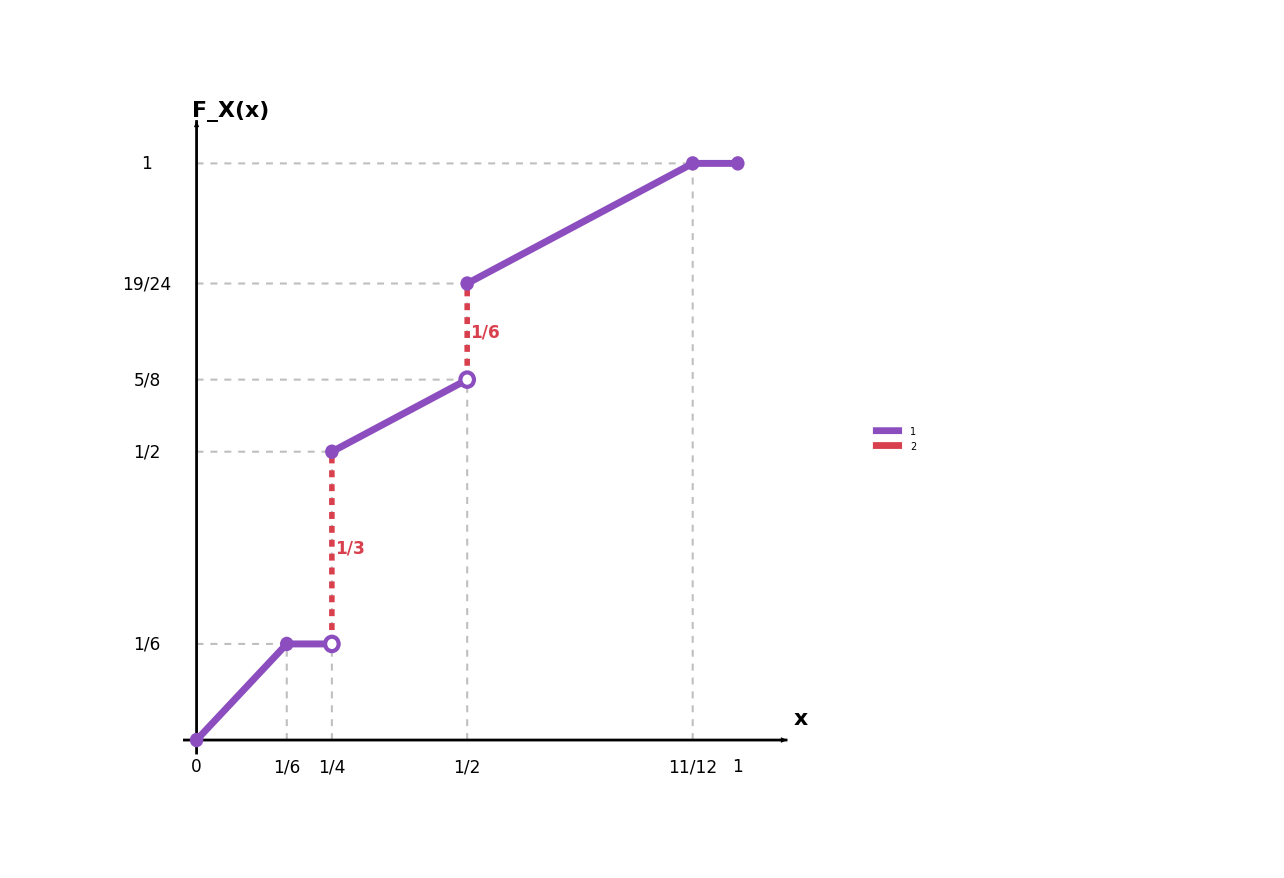

```mathematica
ClearAll[colCDF, colSalto, colPto, r, cerrado, abierto, ejes, guiasL, saltosL, curvaL, puntosL, etiquetasL, graficoL, diagramaL];

colCDF = RGBColor[0.55, 0.3, 0.75];
colSalto = RGBColor[0.85, 0.25, 0.3];
colPto = RGBColor[0.95, 0.6, 0.15];
r = 0.3;

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {26.2, 0}}], Arrow[{{0, -0.6}, {0, 25.8}}]} ;

(* Guías punteadas para niveles de F_X *)
guiasL = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Line[{{4, 0}, {4, 4}}], Line[{{0, 4}, {6, 4}}],
   Line[{{6, 0}, {6, 12}}], Line[{{0, 12}, {6, 12}}],
   Line[{{12, 0}, {12, 19}}], Line[{{0, 15}, {12, 15}}], Line[{{0, 19}, {12, 19}}],
   Line[{{22, 0}, {22, 24}}], Line[{{0, 24}, {24, 24}}]};

(* Curva continua a trozos de F_X bajo Lebesgue *)
curvaL = {colCDF, AbsoluteThickness[5],
   Line[{{0, 0}, {4, 4}}], Line[{{4, 4}, {6, 4}}],
   Line[{{6, 12}, {12, 15}}], Line[{{12, 19}, {22, 24}}],
   Line[{{22, 24}, {24, 24}}]};

(* Saltos en las masas puntuales *)
saltosL = {colSalto, Dashed, AbsoluteThickness[4],
   Line[{{6, 4}, {6, 12}}], Line[{{12, 15}, {12, 19}}]};

puntosL = {
   cerrado[{0, 0}, colCDF], cerrado[{4, 4}, colCDF],
   abierto[{6, 4}, colCDF], cerrado[{6, 12}, colCDF],
   abierto[{12, 15}, colCDF], cerrado[{12, 19}, colCDF],
   cerrado[{22, 24}, colCDF], cerrado[{24, 24}, colCDF]
};

etiquetasL = {Black,
   Table[Text[Style[p[[2]], 17], {p[[1]], -1.1}],
    {p, {{0, "0"}, {4, "1/6"}, {6, "1/4"}, {12, "1/2"}, {22, "11/12"}, {24, "1"}}}] ,
   Table[Text[Style[p[[2]], 17], {-2.2, p[[1]]}],
    {p, {{4, "1/6"}, {12, "1/2"}, {15, "5/8"}, {19, "19/24"}, {24, "1"}}}] ,
   Text[Style["x", 22, Bold], {26.8, 0.9}],
   Text[Style[Row[{Subscript["F", "X"], "(x)"}], 22, Bold], {1.5, 26.2}],
   Text[Style["1/3", 17, Bold, colSalto], {6.8, 8.0}],
   Text[Style["1/6", 17, Bold, colSalto], {12.8, 17.0}]};

graficoL = Graphics[{guiasL, ejes, saltosL, curvaL, puntosL, etiquetasL},
   PlotRange -> {{-3.8, 28.5}, {-2.4, 27.5}}, ImageSize -> 950];

diagramaL = Legended[graficoL,
   SwatchLegend[{colCDF, colSalto}, {"función de distribución", "saltos (masas puntuales)"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagramaL

Export[CloudObject["T3_PAd1_FX"], diagramaL, "PNG", Background -> None, ImageResolution -> 300];
```